## Companion code for the paper “Stars In Their Constellations: Great person or great team?” by Mindruta, Bercovitz, Mares, and Feldman. This notebook calculates the point estimates and 95% confidence intervals. Results are reported in Table 2a of the paper. The notebook was created in Mathematica 12.3. init

```mathematica
SetDirectory[NotebookDirectory[]];
directory="https://raw.githubusercontent.com/MaximumScoreEstimator/MSE-Mathematica/stars/";
Get[directory<>"mse.m"]
```

Loaded import.m

Loaded payoff.m

Loaded matching.m

Loaded inequalities.m

Loaded dataArray.m

Loaded objective.m

Loaded maximize.m

Loaded confidence.m

Loaded modifydata.m

{170433944,143096600,1}

## Import precomputed data

Load the data

```mathematica
filename="../data/stars_replication_step1.dat";
```

```mathematica
import[filename,"precomp"];
{header,noM,noU,noD,noAttr,distanceMatrices,matchMatrix,mate}
```

{{market,upstreamid,downstreamid,cites_cites,cites_size,kn_similarity,_sq (kn_similarity),domain_similarity,cites_rankcmd,cites_experience,match},33,4,{{{0,0,1,0,0,0,0,0,0},8},31,{1}},{{{{1},{2},{3},{4},{5},{6},{7},{8},{9}},{{3},{4},{2},{9},{7},{8},{6},{1},{5}}},31,{{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}},{{10},{1},{3},{8},{6},{2,12},{7},{11},{5},{4,9}}}}}
 |  |  |  |

## Routines (calculate payoff matrix, inequalities members, dataArray)

```mathematica
CpayoffMatrix[payoffDM,noM,noU,noD];
```

```mathematica
Cineqmembers[mate];
```

```mathematica
CdataArray[payoffMatrix,Cx[noAttr-1]];
```

## Maximization

### Differential Evolution Method

The default DifferentialEvolution parameters:

option name | default value |  
"CrossProbability" | 0.5 | probability that a gene is taken from x_i
"InitialPoints" | Automatic | set of initial points 
"PenaltyFunction" | Automatic | function applied to constraints to penalize invalid points
"PostProcess" | Automatic | whether to post-process using local search methods 
"RandomSeed" | 0 | starting value for the random number generator
"ScalingFactor" | 0.6 | scale applied to the difference vector in creating a mate 
"SearchPoints" | Automatic | size of the population used for evolution 
"Tolerance" | 0.001 | tolerance for accepting constraint violations

```mathematica
?maximize
```

```mathematica
method={"DifferentialEvolution","CrossProbability"->0.5,"InitialPoints"->Automatic,"PenaltyFunction"->Automatic,"PostProcess"->Automatic,"RandomSeed"->12,"ScalingFactor"->0.6,"SearchPoints"->300,"Tolerance"->0.001};
sol=maximize[dataArray,noAttr,method];
```

The new ordering of attributes used for calculating the solutio order={5,6,1,3,2,4}

Method {DifferentialEvolution, CrossProbability -> 0.5, InitialPoints -> Automatic, PenaltyFunction -> Automatic, PostProcess -> Automatic, RandomSeed -> 12, ScalingFactor -> 0.6, SearchPoints -> 300, Tolerance -> 0.001}

Completed : {Number of satisfied inequalities→3731.,{cites_size→0.0664202,kn_similarity→4.98191,_sq (kn_similarity)→-2.40165,domain_similarity→2.76088,cites_rankcmd→1.39831,cites_experience→1.28895},Number of inequalities→3745}
Satisfied Ineqs Analysis:
 Market no | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33
Satisfied | 36 | 66 | 20 | 36 | 28 | 21 | 21 | 55 | 15 | 66 | 208 | 28 | 90 | 209 | 21 | 55 | 209 | 104 | 91 | 276 | 44 | 149 | 170 | 66 | 153 | 435 | 28 | 153 | 231 | 105 | 120 | 377 | 45
Total | 36 | 66 | 21 | 36 | 28 | 21 | 21 | 55 | 15 | 66 | 210 | 28 | 91 | 210 | 21 | 55 | 210 | 105 | 91 | 276 | 45 | 153 | 171 | 66 | 153 | 435 | 28 | 153 | 231 | 105 | 120 | 378 | 45
Percentage % | 100 | 100 | 95 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 99 | 100 | 99 | 100 | 100 | 100 | 100 | 99 | 100 | 100 | 98 | 97 | 99 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100

## Confidence Intervals

### execution

```mathematica
ssSize=28;numSubsamples=2500;alpha=0.05;
```

```mathematica
(*If you want to calculate confidence intervals with other subSamples please uncomment the code below*)
(*
(Print["Starting pointIdentified process where alpha = ",alpha];
pointIdentified=pointIdentifiedCR[ssSize,numSubsamples,sol[[2]], Cx[noAttr-1], groupIDs, dataArray,method,True,confidenceLevel->(1-alpha),asymptotics->nests, progressUpdate->10];
{pointIdentified,
ListPlot@Flatten[Map[
MapIndexed[Flatten@{#2,#1}&,#]&,
pointIdentified[[-1]]
],1]
})//AbsoluteTiming
*)
```

```mathematica
(*If you need to save the calculated list of subSamples please uncomment the code below. This is rarely necessary in practice and we included here for reproducibility reasons *)
(*
savedGroups=randomGroups;
savedGroups>>"savedGroups.m";
savedGroups
savedGroups=.; (*clears the variable*)
*)
```

#### Run with saved subSamples (Random Groups) (*This step is provided in the code for reproducibility reasons. Running the confidence intervals using the saved random groups allows users to obtain the same results as in Table 2a of the paper. Skip this step if you want to generate the confidence intervals with own set of subsamples *)

```mathematica
savedGroups=<<"../data/savedGroupsReplication.m";
numSubsamples=Length[savedGroups]
```

2500

Starting pointIdentified process where alpha = 0.05

Iterations completed:10

Iterations completed:20

Iterations completed:30

Iterations completed:40

Iterations completed:50

Iterations completed:60

Iterations completed:70

Iterations completed:80

Iterations completed:90

Iterations completed:100

Iterations completed:110

Iterations completed:120

Iterations completed:130

Iterations completed:140

Iterations completed:150

Iterations completed:160

Iterations completed:170

Iterations completed:180

Iterations completed:190

Iterations completed:200

Iterations completed:210

Iterations completed:220

Iterations completed:230

Iterations completed:240

Iterations completed:250

Iterations completed:260

Iterations completed:270

Iterations completed:280

Iterations completed:290

Iterations completed:300

Iterations completed:310

Iterations completed:320

Iterations completed:330

Iterations completed:340

Iterations completed:350

Iterations completed:360

Iterations completed:370

Iterations completed:380

Iterations completed:390

Iterations completed:400

Iterations completed:410

Iterations completed:420

Iterations completed:430

Iterations completed:440

Iterations completed:450

Iterations completed:460

Iterations completed:470

Iterations completed:480

Iterations completed:490

Iterations completed:500

Iterations completed:510

Iterations completed:520

Iterations completed:530

Iterations completed:540

Iterations completed:550

Iterations completed:560

Iterations completed:570

Iterations completed:580

Iterations completed:590

Iterations completed:600

Iterations completed:610

Iterations completed:620

Iterations completed:630

Iterations completed:640

Iterations completed:650

Iterations completed:660

Iterations completed:670

Iterations completed:680

Iterations completed:690

Iterations completed:700

Iterations completed:710

Iterations completed:720

Iterations completed:730

Iterations completed:740

Iterations completed:750

Iterations completed:760

Iterations completed:770

Iterations completed:780

Iterations completed:790

Iterations completed:800

Iterations completed:810

Iterations completed:820

Iterations completed:830

Iterations completed:840

Iterations completed:850

Iterations completed:860

Iterations completed:870

Iterations completed:880

Iterations completed:890

Iterations completed:900

Iterations completed:910

Iterations completed:920

Iterations completed:930

Iterations completed:940

Iterations completed:950

Iterations completed:960

Iterations completed:970

Iterations completed:980

Iterations completed:990

Iterations completed:1000

Iterations completed:1010

Iterations completed:1020

Iterations completed:1030

Iterations completed:1040

Iterations completed:1050

Iterations completed:1060

Iterations completed:1070

Iterations completed:1080

Iterations completed:1090

Iterations completed:1100

Iterations completed:1110

Iterations completed:1120

Iterations completed:1130

Iterations completed:1140

Iterations completed:1150

Iterations completed:1160

Iterations completed:1170

Iterations completed:1180

Iterations completed:1190

Iterations completed:1200

Iterations completed:1210

Iterations completed:1220

Iterations completed:1230

Iterations completed:1240

Iterations completed:1250

Iterations completed:1260

Iterations completed:1270

Iterations completed:1280

Iterations completed:1290

Iterations completed:1300

Iterations completed:1310

Iterations completed:1320

Iterations completed:1330

Iterations completed:1340

Iterations completed:1350

Iterations completed:1360

Iterations completed:1370

Iterations completed:1380

Iterations completed:1390

Iterations completed:1400

Iterations completed:1410

Iterations completed:1420

Iterations completed:1430

Iterations completed:1440

Iterations completed:1450

Iterations completed:1460

Iterations completed:1470

Iterations completed:1480

Iterations completed:1490

Iterations completed:1500

Iterations completed:1510

Iterations completed:1520

Iterations completed:1530

Iterations completed:1540

Iterations completed:1550

Iterations completed:1560

Iterations completed:1570

Iterations completed:1580

Iterations completed:1590

Iterations completed:1600

Iterations completed:1610

Iterations completed:1620

Iterations completed:1630

Iterations completed:1640

Iterations completed:1650

Iterations completed:1660

Iterations completed:1670

Iterations completed:1680

Iterations completed:1690

Iterations completed:1700

Iterations completed:1710

Iterations completed:1720

Iterations completed:1730

Iterations completed:1740

Iterations completed:1750

Iterations completed:1760

Iterations completed:1770

Iterations completed:1780

Iterations completed:1790

Iterations completed:1800

Iterations completed:1810

Iterations completed:1820

Iterations completed:1830

Iterations completed:1840

Iterations completed:1850

Iterations completed:1860

Iterations completed:1870

Iterations completed:1880

Iterations completed:1890

Iterations completed:1900

Iterations completed:1910

Iterations completed:1920

Iterations completed:1930

Iterations completed:1940

Iterations completed:1950

Iterations completed:1960

Iterations completed:1970

Iterations completed:1980

Iterations completed:1990

Iterations completed:2000

Iterations completed:2010

Iterations completed:2020

Iterations completed:2030

Iterations completed:2040

Iterations completed:2050

Iterations completed:2060

Iterations completed:2070

Iterations completed:2080

Iterations completed:2090

Iterations completed:2100

Iterations completed:2110

Iterations completed:2120

Iterations completed:2130

Iterations completed:2140

Iterations completed:2150

Iterations completed:2160

Iterations completed:2170

Iterations completed:2180

Iterations completed:2190

Iterations completed:2200

Iterations completed:2210

Iterations completed:2220

Iterations completed:2230

Iterations completed:2240

Iterations completed:2250

Iterations completed:2260

Iterations completed:2270

Iterations completed:2280

Iterations completed:2290

Iterations completed:2300

Iterations completed:2310

Iterations completed:2320

Iterations completed:2330

Iterations completed:2340

Iterations completed:2350

Iterations completed:2360

Iterations completed:2370

Iterations completed:2380

Iterations completed:2390

Iterations completed:2400

Iterations completed:2410

Iterations completed:2420

Iterations completed:2430

Iterations completed:2440

Iterations completed:2450

Iterations completed:2460

Iterations completed:2470

Iterations completed:2480

Iterations completed:2490

Iterations completed:2500

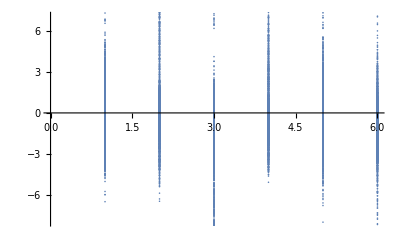
{39047.7,{{{Symmetric case,{cites_size→{-1.11253,1.24537},kn_similarity→{1.17504,8.78877},_sq (kn_similarity)→{-5.15501,0.351712},domain_similarity→{1.29521,4.22655},cites_rankcmd→{0.158782,2.63784},cites_experience→{0.0345273,2.54337}}},{{0.558197,5.28437,-2.97621,2.42681,2.8972,0.606419},{0.188409,10.9795,-7.84626,2.96321,3.81999,-4.34684},{-2.41274,-1.41615,1.27473,-1.29011,-0.212491,-3.70627},{6.82626,16.6789,-7.97382,9.00454,-0.451895,-1.28683},{4.90732,19.3004,-13.3832,7.81302,3.36264,3.17533},2490,{-3.69956,-1.34085,0.517574,-1.0584,1.25866,-1.94484},{3.47271,-0.709188,0.671019,-0.0861128,-2.75086,-1.74867},{1.29719,9.18486,-5.89605,3.72432,3.64856,0.794834},{1.64222,-0.212778,-0.623831,-0.424074,-1.20597,-2.40793},{2.25721,0.222333,-0.592207,-2.17524,0.48012,-0.301569}}},-Graphics-}}
 |  |  |  |

```mathematica
(Print["Starting pointIdentified process where alpha = ",alpha];
pointIdentified=pointIdentifiedCR[ssSize,numSubsamples,sol[[2]], Cx[noAttr-1], groupIDs, dataArray,method,True,confidenceLevel->(1-alpha),asymptotics->nests, progressUpdate->10,useSavedGroups->True];
{{pointIdentified[[1,1]],pointIdentified[[2]]},
ListPlot@Flatten[Map[
MapIndexed[Flatten@{#2,#1}&,#]&,
pointIdentified[[-1]]
],1]
})//AbsoluteTiming

(*Attention: the graph plots all point estimates, regardless of whether they fall or not in the confidence intervals*)
```

```mathematica
Export["C:\\Users\\mindruta\\Documents\\RESEARCH\\msework\\Remove\\RemoveMultipleRun\\starsreplicationCIsolutions.dat",pointIdentified[[-1]]]; (* 
Export["../data/starsreplicationCIsolutions.dat",pointIdentified[[-1]]];
Saves all solutions (point-identified estimates) in the confidence intervals; the file serves as input in the robustness checks analysis- see Appendix 2 of the paper  *)
```